```mathematica
LOptions[f_]:=Block[{t1=Table[BooleanMinimize[f,m],{m,{"DNF","CNF","POS","ANF","AND","OR"}}]},Block[{t2=Map[FullSimplify[#,TimeConstraint->Infinity,ExcludedForms->{_⊽_,_⇒_,_⊼_}]&,t1]},{Column[t1],Column[t2]}]]
```

```mathematica
eTrue=1;
xTrue=1;
nTrue=1;
allTrue=1;
```

```mathematica
func[e_,n_,z_]:={e,n,z}->Piecewise[{{z, e==eTrue}, {Piecewise[{{Piecewise[{{allTrue, xTrue==n}, {1-allTrue, xTrue≠n}}], nTrue==1}, {Piecewise[{{1-allTrue, xTrue==n}, {allTrue, xTrue≠n}}], nTrue==0}}], e≠eTrue}}]
```

```mathematica
func[e_,n_,z_,x_,eTrue_,xTrue_,nTrue_,allTrue_]:={e,n,z}->Piecewise[{{z, e==eTrue}, {Piecewise[{{Piecewise[{{allTrue, x==n}, {1-allTrue, x≠n}}], nTrue==1}, {Piecewise[{{1-allTrue, x==n}, {allTrue, x≠n}}], nTrue==0}}], e≠eTrue}}]
mfs[eTrue_,xTrue_,nTrue_,allTrue_]:=
Block[{bf=BooleanFunction[Flatten[Table[func[a,b,c,d,eTrue,xTrue,nTrue,allTrue],{a,0,1},{b,0,1},{c,0,1},{d,0,1}]]]},
Block[{t1=Table[BooleanMinimize[bf,m][e,n,z,x],{m,{"DNF","CNF","POS","ANF","AND","OR"}}]},
Block[{t2=Map[FullSimplify[#,TimeConstraint->Infinity,ExcludedForms->{_⊽_,_⇒_,_⊼_}]&,t1]},
{Column[t1],Column[t2]}]]]
```

```mathematica
f2[e_,n_,z_,x_]:=Piecewise[{{z, e==1}, {Piecewise[{{z, x==n}, {1, x≠n}}], e==0}}]
bf2=BooleanFunction[Flatten[Table[f2[a,b,c,d],{a,0,1},{b,0,1},{c,0,1},{d,0,1}]]];
t12=Table[BooleanMinimize[bf2,m][e,n,z,x],{m,{"DNF","CNF","POS","ANF","AND","OR"}}];
t22=Map[FullSimplify[#,TimeConstraint->Infinity,ExcludedForms->{_⊽_,_⇒_,_⊼_}]&,t12];
{Column[t12],Column[t22]}
```

{(e&&n&&!x)||(e&&!n&&x)||!z
(e||!z)&&(!n||!z||!x)&&(n||!z||x)
(e||!z)&&(!n||!z||!x)&&(n||!z||x)
!(z⊻(e&&n&&z)⊻(e&&z&&x))
!(!e&&z)&&!(n&&z&&x)&&!(!n&&z&&!x)
!(!e||!n||x)||!(!e||n||!x)||!z,!(z⊻(e&&n&&z)⊻(e&&x&&z))
!(z⊻(e&&n&&z)⊻(e&&x&&z))
!(z⊻(e&&n&&z)⊻(e&&x&&z))
!(z⊻(e&&n&&z)⊻(e&&z&&x))
!(z⊻(e&&n&&z)⊻(e&&x&&z))
!(z⊻(e&&n&&z)⊻(e&&x&&z))}

```mathematica
BooleanTable[{f2[Boole[¬e],Boole[¬n],Boole[¬z],Boole[¬x]],Boole[(e&&n&&!x)||(e&&!n&&x)||!z]},{e,n,z,x}]
```

{{0,0},{1,1},{1,1},{1,1},{1,1},{0,0},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1}}

```mathematica
FullSimplify[((¬e)&&(¬n)&&!(¬x))||((¬e)&&!(¬n)&&(¬x))||!(¬z)]
```

(!e&&!n&&x)||(!e&&n&&!x)||z

```mathematica
(!True&&!n&&x)||(!True&&n&&!x)||z==z
```

True

```mathematica
TableForm[BooleanTable[{"e",1-Boole[e],"n",1-Boole[n],"x",1-Boole[x],"z",1-Boole[z],"y",Boole[(e&&n&&!x)||(e&&!n&&x)||!z]},{e,n,z,x}]]
```

e | 0 | n | 0 | x | 0 | z | 0 | y | 0
e | 0 | n | 0 | x | 1 | z | 0 | y | 1
e | 0 | n | 0 | x | 0 | z | 1 | y | 1
e | 0 | n | 0 | x | 1 | z | 1 | y | 1
e | 0 | n | 1 | x | 0 | z | 0 | y | 1
e | 0 | n | 1 | x | 1 | z | 0 | y | 0
e | 0 | n | 1 | x | 0 | z | 1 | y | 1
e | 0 | n | 1 | x | 1 | z | 1 | y | 1
e | 1 | n | 0 | x | 0 | z | 0 | y | 0
e | 1 | n | 0 | x | 1 | z | 0 | y | 0
e | 1 | n | 0 | x | 0 | z | 1 | y | 1
e | 1 | n | 0 | x | 1 | z | 1 | y | 1
e | 1 | n | 1 | x | 0 | z | 0 | y | 0
e | 1 | n | 1 | x | 1 | z | 0 | y | 0
e | 1 | n | 1 | x | 0 | z | 1 | y | 1
e | 1 | n | 1 | x | 1 | z | 1 | y | 1

```mathematica
(!e&&!n&&x)||(!e&&n&&!x)||z
```

```mathematica
"If e, then output z.";
(!True&&!n&&x)||(!True&&n&&!x)||z==z
```

True

```mathematica
"If not e...";
(!False&&!n&&x)||(!False&&n&&!x)||z
```

(!n&&x)||(n&&!x)||z

```mathematica
"If x == n, output z.";
FullSimplify[(!n&&n)||(n&&!n)||z]
```

z

```mathematica
"Else, if x /= n, output 1.";
FullSimplify[(!n&&(¬n))||(n&&!(¬n))||z]
```

True

```mathematica
"
For this code, we have a set of And/Not formulas and want to stop traversing down a branch if any of them evaluate to False.

Formulas are of the form: (L1 && L2 &&...), where Li may be either Vi or ~Vi, and Vi is the ith variable.

(Variable index is implicit in all these definitions and calculations, i.e. . To convert to using 'i' as the variable index, simply add '[i]' to the end of all variables.)

Definitions:

True  = 1
False = 0

g = ~P | y

y = (~e & ~n & x) | (~e & n & ~x) | z
  where:
    g = are all formulas good, i.e. either incomplete or true?
    x = current edge orientation (1 if [e1,e2]->e1<e2, else 0)
    y = current sofar
      0 -> invalid or   possible invalid
      1 -> valid   or impossible invalid
    z = previous sofar:
    e = P | ~I
    P = 1 if past the end of the formula, else 0
    I = 1 if position within the formula, else 0
    n = 1 if position ~ed in the formula, else 0

These definitions and formulas satisfy the following properties:

  If the formula is incomplete or invalid, 'g' is True.

  If past the end of the formula or the current variable is not part of the formula, i.e. 'e' is True,
    then the next equals the current: y = (~1 & ~n & x) | (~1 & n & ~x) | z = z
    else if both ~ed and backward or neither ~ed nor backward
      then the next equals the current: (~0 & ~n & n) | (~0 & n & ~n) | z = z
      else the formula cannot be satisfied and the next is '1': (~0 & ~n & (~n)) | (~0 & n & ~(~n)) | z = 1

  Because the implementation assumes constant [x,e,P,I,n], we can define A = (~e & ~n & x) | (~e & n & ~x) and reduce calculating 'y' to a single operation (y = A | z), and similarily reduce calculating 'g' (g = (~P) | y).

To implement this one makes the following replacements ('i' is variable index, 'j' is formula index):
  g -> g[j]
  x -> x[i]
  y -> y[i][j]
  z -> z[i][j]
  etc.

Assuming a 64-bit CPU, 
  G = (g[i] == ONES), a reduction of g[i] to a single Bool
  ONES = 2^64-1, where the lengths of 'g[i]' and 'ONES' are equal

Assuming 'v' variables, 'f' formulas, and 'c' checks, the resulting algorithm (not including 'x[]') uses
  space = (size of A's) + (size of (~P)'s) + (size of y[i]'s) + (size of g[i])
  space = ( v*f bits  ) + ( v*f bits     ) + ( v*f bits     ) + ( 0 bits     )
  space = 3*v*f bits

  time  = (number of G's calculated) + (number of y's calculated)
  time  = 2*c*f assembly operations

Note: These values should be adapted to qword (64-bit word) sizes.

In using this algorithm to optimize Maxcy, the trick is to get as close to possible to taking time == time saved by formulas.
For this to happen, one wants f*(fraction not satisfying)*2^v == time saved, where the fraction not satisfying is deduced from the number of strong orientations relative to '2^v'.

Because finding the number of strong orientations is a P#-Complete problem, the reasonable course of action is to estimate the number of strong orientations and use that to calculate how many formulas to use.

For computing 'G', first note that 'g[i] == ONES' is equivalent to '~g[i] > 0' and nonzero integers may be interpreted as True in C code. Because of this, we make the following derivation to a faster implementation:
  G = ((~P[0] | y[0]) == ONES) | ((~P[1] | y[1]) == ONES) | ... | ((~P[2] | y[2]) == ONES) [4*f-1 operations with at least 3 registers]
  G = ~g[0] | ~g[1] | ~g[2] | ... | ~g[f-1]
  G = ~(~P[0] | y[0]) | ... | ~(~P[f-1] | y[f-1])
  G = (P[0] & ~y[0]) | ... | (P[f-1] & ~y[f-1]) [2*f operations with at least 2 registers]
";
```

```mathematica
"3*Ceiling[f/64] operations per lookup.";
```

```mathematica
LOptions[(!p0 && !y0) || (!p1 && !y1)||(!p2 && !y2)]
```

{(!p0&&!y0)||(!p1&&!y1)||(!p2&&!y2)
(!p0||!p1||!p2)&&(!p0||!p1||!y2)&&(!p0||!p2||!y1)&&(!p0||!y1||!y2)&&(!p1||!p2||!y0)&&(!p1||!y0||!y2)&&(!p2||!y0||!y1)&&(!y0||!y1||!y2)
(!p0||!p1||!p2)&&(!p0||!p1||!y2)&&(!p0||!p2||!y1)&&(!p0||!y1||!y2)&&(!p1||!p2||!y0)&&(!p1||!y0||!y2)&&(!p2||!y0||!y1)&&(!y0||!y1||!y2)
!((p0&&p1&&p2)⊻(p0&&p1&&y2)⊻(p0&&p2&&y1)⊻(p0&&y1&&y2)⊻(p1&&p2&&y0)⊻(p1&&y0&&y2)⊻(p2&&y0&&y1)⊻(y0&&y1&&y2)⊻(p0&&p1&&p2&&y0)⊻(p0&&p1&&p2&&y1)⊻(p0&&p1&&p2&&y2)⊻(p0&&p1&&y0&&y2)⊻(p0&&p1&&y1&&y2)⊻(p0&&p2&&y0&&y1)⊻(p0&&p2&&y1&&y2)⊻(p0&&y0&&y1&&y2)⊻(p1&&p2&&y0&&y1)⊻(p1&&p2&&y0&&y2)⊻(p1&&y0&&y1&&y2)⊻(p2&&y0&&y1&&y2)⊻(p0&&p1&&p2&&y0&&y1)⊻(p0&&p1&&p2&&y0&&y2)⊻(p0&&p1&&p2&&y1&&y2)⊻(p0&&p1&&y0&&y1&&y2)⊻(p0&&p2&&y0&&y1&&y2)⊻(p1&&p2&&y0&&y1&&y2)⊻(p0&&p1&&p2&&y0&&y1&&y2))
!(p0&&p1&&p2)&&!(p0&&p1&&y2)&&!(p0&&p2&&y1)&&!(p0&&y1&&y2)&&!(p1&&p2&&y0)&&!(p1&&y0&&y2)&&!(p2&&y0&&y1)&&!(y0&&y1&&y2)
!(p0||y0)||!(p1||y1)||!(p2||y2),(!p0&&!y0)||(!p1&&!y1)||(!p2&&!y2)
(!p0&&!y0)||(!p1&&!y1)||(!p2&&!y2)
(!p0&&!y0)||(!p1&&!y1)||(!p2&&!y2)
(!p0&&!y0)||(!p1&&!y1)||(!p2&&!y2)
(!p0&&!y0)||(!p1&&!y1)||(!p2&&!y2)
!(p0||y0)||!(p1||y1)||!(p2||y2)}

```mathematica
f2[e_,n_,z_,x_]:=Piecewise[{{z, e==1}, {Piecewise[{{z, x==n}, {1, x≠n}}], e==0}}]
```

```mathematica
(!e&&!n&&x)||(!e&&n&&!x)||z
"If e, then output z.";
(!True&&!n&&x)||(!True&&n&&!x)||z==z
True
"If not e...";
(!False&&!n&&x)||(!False&&n&&!x)||z
(!n&&x)||(n&&!x)||z
"If x == n, output z.";
FullSimplify[(!n&&n)||(n&&!n)||z]
z
"Else, if x /= n, output 1.";
FullSimplify[(!n&&(¬n))||(n&&!(¬n))||z]
True
```

```mathematica
ConnectedComponents[g]
```

```mathematica
"There are 3*Ceiling[f/64]*c + f == steps to check whether 'c' mixed orientations are 'good'. We want this to be maximized relative to '#uCy*(2^e-#kXo)' and we already (at this point) have #uCy.";
"#uCy = # of directed cycles in the undirected graph";
"#kXo = # of k-escapable orientations";
"(3*Ceiling[f/64]*#kXo  +  #kXo + #kXo*#uCy)/(#uCy*SuperscriptBox[2, e]) < 1?";
```

```mathematica
"It is NP-Complete to decide whether a mixed graph has a strong orientation: http://www.sciencedirect.com/science/article/pii/S0166218X01002281";
```

```mathematica
"Randomized algorithms: http://www.tau.ac.il/~nogaa/PDFS/afw9.pdf (p.12)";

"Requires Ceiling[ϵ^-22^Ceiling[4/α]] steps, where MinDegree[g] == δ[G] ≤ αn == α(# of vertices).";
```

```mathematica
fold1Esc[sofar_,l_]:=Block[{g=Graph[l]},sofar+Boole[Fold[#1*#2&,1,VertexInDegree[g]*VertexOutDegree[g]]≠0]]
count1Esc[graph_]:=Block[{el=EdgeList[graph]},
Block[{len=Length[el]},
Fold[fold1Esc,0,Table[nthOriantation[graph,j,el,len],{j,1,2^len-1}]]]]
```

```mathematica
Timing[Monitor[count1Esc[CompleteGraph[3]],j]]
```

{0.00183,2}

```mathematica
Timing[Monitor[count1Esc[CompleteGraph[4]],j]]
```

{0.008481,24}

```mathematica
Timing[Monitor[count1Esc[CompleteGraph[5]],j]]
```

{0.152927,544}

```mathematica
Timing[Monitor[count1Esc[CompleteGraph[6]],j]]
```

{5.62943,22400}

```mathematica
Timing[Monitor[count1Esc[CompleteGraph[7]],j]]
```

{443.465,1681408}

```mathematica
Timing[Monitor[count1Esc[WheelGraph[4]],j]]
```

{0.008447,24}

```mathematica
Timing[Monitor[count1Esc[WheelGraph[5]],j]]
```

{0.038486,78}

```mathematica
Timing[Monitor[count1Esc[WheelGraph[6]],j]]
```

{0.148901,240}

```mathematica
Timing[Monitor[count1Esc[WheelGraph[7]],j]]
```

{0.663676,726}

```mathematica
Timing[Monitor[count1Esc[WheelGraph[8]],j]]
```

{2.75387,2184}

```mathematica
Timing[Monitor[count1Esc[WheelGraph[9]],j]]
```

{11.7193,6558}

```mathematica
Timing[Monitor[count1Esc[WheelGraph[10]],j]]
```

{50.0364,19680}

```mathematica
"http://oeis.org/A058809";
```

```mathematica
wg1p=Join[{0},LinearRecurrence[{4,-3},{0,6},50]]
```

{0,0,6,24,78,240,726,2184,6558,19680,59046,177144,531438,1594320,4782966,14348904,43046718,129140160,387420486,1162261464,3486784398,10460353200,31381059606,94143178824,282429536478,847288609440,2541865828326,7625597484984,22876792454958,68630377364880,205891132094646,617673396283944,1853020188851838,5559060566555520,16677181699666566,50031545098999704,150094635296999118,450283905890997360,1350851717672992086,4052555153018976264,12157665459056928798,36472996377170786400,109418989131512359206,328256967394537077624,984770902183611232878,2954312706550833698640,8862938119652501095926,26588814358957503287784,79766443076872509863358,239299329230617529590080,717897987691852588770246}

```mathematica
FindGeneratingFunction[wg1p,x]
```

(6 x^2)/(1-4 x+3 x^2)

```mathematica
FindGeneratingFunction[wg1,x]
```

(6 x^2)/(1-4 x+3 x^2)

```mathematica
Factor[(6 x^2)/(1-4 x+3 x^2)]
```

```mathematica
Expand[(6 x^2)/((-1+x) (-1+3 x))]
```

(6 x^2)/((-1+x) (-1+3 x))

```mathematica
Total[Table[x^(i-3)*wg1[[i]],{i,1,Length[wg1]}]]
```

6+24 x+78 x^2+240 x^3+726 x^4+2184 x^5+6558 x^6+19680 x^7+59046 x^8+177144 x^9+531438 x^10+1594320 x^11+4782966 x^12+14348904 x^13+43046718 x^14+129140160 x^15+387420486 x^16+1162261464 x^17+3486784398 x^18+10460353200 x^19+31381059606 x^20+94143178824 x^21+282429536478 x^22+847288609440 x^23+2541865828326 x^24+7625597484984 x^25+22876792454958 x^26+68630377364880 x^27+205891132094646 x^28

```mathematica
Table[{{24,78,240,726,2184,6558,19680}[[i]],2^Length[EdgeList[WheelGraph[i+3]]]},{i,1,7}]
```

{{24,64},{78,256},{240,1024},{726,4096},{2184,16384},{6558,65536},{19680,262144}}

```mathematica
Table[N[{24,78,240,726,2184,6558,19680}[[i]]*2^(-Length[EdgeList[WheelGraph[i+3]]])],{i,1,7}]
```

{0.375,0.304688,0.234375,0.177246,0.133301,0.100067,0.0750732}

```mathematica
rev[e_,dir_]:=Piecewise[{{e[[1]]->e[[2]], dir==0}, {e[[2]]->e[[1]], dir==1}}]
nthOriantation[g_,n0_,el_,len_]:=Block[{n=PadLeft[IntegerDigits[n0,2],len]},
Table[rev[el[[i]],n[[i]]],{i,1,len}]]
eq1[x_]:=Boole[x==1]
countOrientations[sofar_,b_]:=sofar+eq1[Length[ConnectedComponents[Graph[b]]]]

countStrongOrientations[graph_]:=Block[{el=EdgeList[graph]},
Block[{len=Length[el]},
Fold[countOrientations,0,Table[nthOriantation[graph,j,el,len],{j,1,2^len-1}]]]]
```

```mathematica
nthOriantation[CycleGraph[3],0,EdgeList[CycleGraph[3]],3]
```

{1->2,1->3,2->3}

```mathematica
countOrientations[0,nthOriantation[CycleGraph[3],0,EdgeList[CycleGraph[3]],3]]
```

0

```mathematica
countStrongOrientations[CycleGraph[3]]
```

2

```mathematica
Timing[Monitor[countStrongOrientations[CompleteGraph[6]],j]]
```

{5.57437,22320}

```mathematica
Timing[Monitor[countStrongOrientations[CompleteGraph[3]],j]]
```

{0.001922,2}

```mathematica
Timing[Monitor[countStrongOrientations[CompleteGraph[4]],j]]
```

{0.008218,24}

```mathematica
Timing[Monitor[countStrongOrientations[CompleteGraph[5]],j]]
```

{0.136002,544}

```mathematica
Timing[Monitor[countStrongOrientations[CompleteGraph[6]],j]]
```

{5.28141,22320}

```mathematica
Timing[Monitor[countStrongOrientations[CompleteGraph[7]],j]]
```

{413.913,1677488}

```mathematica
Timing[Monitor[countStrongOrientations[CompleteGraph[8]],j]]
```

```mathematica
Length[EdgeList[CompleteGraph[5]]]==5(5-1)/2
```

True

```mathematica
"http://oeis.org/A054946";
```

```mathematica
{Table[2^(i(i-1)/2),{i,3,8}],Table[2^((i+2)(i+1)/2)-{2,24,544,22320,1677488}[[i]],{i,1,5}]}
```

{{8,64,1024,32768,2097152,268435456},{6,40,480,10448,419664}}

```mathematica
Timing[Monitor[countStrongOrientations[WheelGraph[4]],j]]
```

{0.009104,24}

```mathematica
Timing[Monitor[countStrongOrientations[WheelGraph[5]],j]]
```

{0.033332,78}

```mathematica
Timing[Monitor[countStrongOrientations[WheelGraph[6]],j]]
```

{0.154455,240}

```mathematica
Timing[Monitor[countStrongOrientations[WheelGraph[7]],j]]
```

{0.623812,726}

```mathematica
Timing[Monitor[countStrongOrientations[WheelGraph[8]],j]]
```

{2.76995,2184}

```mathematica
Length[EdgeList[WheelGraph[8]]]
```

14

```mathematica
"This suggests that the 1-esc. orientations of wheel graphs are exactly its strong orientations.";
```

```mathematica
"Below is upper bound";
```

```mathematica
(2*∑_(k=3)^n (Binomial[n,k]*(k)!))
```

2 (-1-n^2+ⅇ Gamma[1+n,1])

```mathematica
ArrayPlot[Map[PadLeft[IntegerDigits[#,2],21]&,{2,24,544,22320,1677488}]]
```

```mathematica
"http://journals.cambridge.org/action/displayAbstract?fromPage=online&aid=5045340&fileId=S0017089500000914";
"This shows that complete graphs have far too many strong orientations for checking r-escapability to be beneficial.";
```

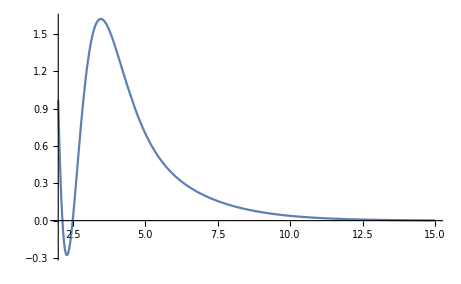

```mathematica
Plot[1-((1-Binomial[n,1] 2^(2-n)+Binomial[n,2] 2^(4-2n)-Binomial[n,3] 2^(8-3n)-Binomial[n,4] 2^(15-4n)+n^5 2^(-5n))),{n,2,15}]
```

```mathematica
FullSimplify[2^-n((2k)^k)^(n/2),{n>0,k>0,Element[n,Integers],Element[k,Integers]}]
```

(2^k k^k)^(n/2)

```mathematica
"From http://link.springer.com/article/10.1007%2FBF02579193, we have that a 2k-regular, n vertex graph has at most √(Binomial[2  k, k]^n) eulerian orientations. Substituting k -> 2k and e -> k n (handshake lemma), we get the following for the maximum probability of a strong orientation:";
```

```mathematica
TableForm[Table[N[2^(-2k n)√(Binomial[4k,2k]^n)],{n,3,10},{k,1,7}]]
```

0.22964 | 0.142984 | 0.107144 | 0.0870258 | 0.0739602 | 0.0647095 | 0.0577732
0.140625 | 0.0747681 | 0.050889 | 0.0385653 | 0.0310454 | 0.0259791 | 0.0223341
0.0861149 | 0.0390972 | 0.0241702 | 0.0170902 | 0.0130316 | 0.0104299 | 0.00863397
0.0527344 | 0.0204444 | 0.0114798 | 0.00757349 | 0.00547011 | 0.00418731 | 0.00333774
0.0322931 | 0.0106906 | 0.00545245 | 0.00335618 | 0.00229612 | 0.00168109 | 0.00129031
0.0197754 | 0.00559026 | 0.00258969 | 0.00148729 | 0.000963817 | 0.000674912 | 0.000498812
0.0121099 | 0.00292322 | 0.00123 | 0.000659089 | 0.00040457 | 0.000270959 | 0.000192832
0.00741577 | 0.00152859 | 0.000584198 | 0.000292074 | 0.000169822 | 0.000108783 | 0.0000745455

```mathematica
"Here are
```

```mathematica
TableForm[Table[N[-Log[2^(-2k n)√(Binomial[4k,2k]^n)]/Log[k n]],{n,3,10},{k,1,7}]]
```

1.33918 | 1.08554 | 1.01655 | 0.982552 | 0.961662 | 0.94723 | 0.936512
1.41504 | 1.24714 | 1.19848 | 1.17414 | 1.15908 | 1.14865 | 1.14088
1.52356 | 1.40785 | 1.37466 | 1.35835 | 1.34842 | 1.34161 | 1.33659
1.64223 | 1.56547 | 1.54553 | 1.53651 | 1.53136 | 1.52802 | 1.52567
1.76416 | 1.7197 | 1.71182 | 1.70966 | 1.70912 | 1.70917 | 1.70945
1.88672 | 1.87072 | 1.87417 | 1.87862 | 1.88258 | 1.88596 | 1.88885
2.00878 | 2.0188 | 2.03309 | 2.04398 | 2.05237 | 2.05906 | 2.06455
2.12984 | 2.16422 | 2.18901 | 2.20623 | 2.219 | 2.22897 | 2.23705

```mathematica
Binomial[4k,2k]~ 4^(2k)/(√(2π k))
Binomial[4k,2k]^n~ 4^(2k n)/(√(2π k))^n
2^(-2k n)√(4^(2k n)/(√(2π k))^n)
```

```mathematica
FullSimplify[Log[2^(-2k n)√(4^(2k n)/(√(2π k))^n)],{n>0,k>0,Element[n,Integers],Element[k,Integers]}]
```

-1/4 n Log[2 k π]

```mathematica
FullSimplify[-1/4 n Log[2 k π]/Log[k n],{n>0,k>0,Element[n,Integers],Element[k,Integers]}]
```

-(n Log[2 k π])/(4 Log[k n])

```mathematica
"Using sterling's appx., we get an upper bound of biggest r-escapable computation that could be beneficial for these graphs.";
```

```mathematica
TableForm[Table[N[(n Log[2 k π])/(4 Log[k n]),2],{n,2,20},{k,2,20}]]
```

0.91 | 0.82 | 0.78 | 0.75 | 0.73 | 0.72 | 0.71 | 0.7 | 0.69 | 0.69 | 0.68 | 0.68 | 0.67 | 0.67 | 0.67 | 0.66 | 0.66 | 0.66 | 0.66
1.1 | 1. | 0.97 | 0.95 | 0.94 | 0.93 | 0.92 | 0.92 | 0.91 | 0.91 | 0.9 | 0.9 | 0.9 | 0.9 | 0.89 | 0.89 | 0.89 | 0.89 | 0.89
1.2 | 1.2 | 1.2 | 1.2 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1 | 1.1
1.4 | 1.4 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3 | 1.3
1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5 | 1.5
1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7 | 1.7
1.8 | 1.8 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9 | 1.9
2. | 2. | 2. | 2. | 2. | 2.1 | 2.1 | 2.1 | 2.1 | 2.1 | 2.1 | 2.1 | 2.1 | 2.1 | 2.1 | 2.1 | 2.1 | 2.1 | 2.1
2.1 | 2.2 | 2.2 | 2.2 | 2.2 | 2.2 | 2.2 | 2.2 | 2.2 | 2.3 | 2.3 | 2.3 | 2.3 | 2.3 | 2.3 | 2.3 | 2.3 | 2.3 | 2.3
2.3 | 2.3 | 2.3 | 2.4 | 2.4 | 2.4 | 2.4 | 2.4 | 2.4 | 2.4 | 2.4 | 2.4 | 2.4 | 2.4 | 2.5 | 2.5 | 2.5 | 2.5 | 2.5
2.4 | 2.5 | 2.5 | 2.5 | 2.5 | 2.6 | 2.6 | 2.6 | 2.6 | 2.6 | 2.6 | 2.6 | 2.6 | 2.6 | 2.6 | 2.6 | 2.6 | 2.6 | 2.6
2.5 | 2.6 | 2.7 | 2.7 | 2.7 | 2.7 | 2.7 | 2.8 | 2.8 | 2.8 | 2.8 | 2.8 | 2.8 | 2.8 | 2.8 | 2.8 | 2.8 | 2.8 | 2.8
2.7 | 2.7 | 2.8 | 2.8 | 2.9 | 2.9 | 2.9 | 2.9 | 2.9 | 2.9 | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3. | 3.
2.8 | 2.9 | 3. | 3. | 3. | 3. | 3.1 | 3.1 | 3.1 | 3.1 | 3.1 | 3.1 | 3.1 | 3.1 | 3.2 | 3.2 | 3.2 | 3.2 | 3.2
2.9 | 3. | 3.1 | 3.1 | 3.2 | 3.2 | 3.2 | 3.2 | 3.3 | 3.3 | 3.3 | 3.3 | 3.3 | 3.3 | 3.3 | 3.3 | 3.3 | 3.3 | 3.4
3.1 | 3.2 | 3.2 | 3.3 | 3.3 | 3.4 | 3.4 | 3.4 | 3.4 | 3.4 | 3.5 | 3.5 | 3.5 | 3.5 | 3.5 | 3.5 | 3.5 | 3.5 | 3.5
3.2 | 3.3 | 3.4 | 3.4 | 3.5 | 3.5 | 3.5 | 3.6 | 3.6 | 3.6 | 3.6 | 3.6 | 3.6 | 3.7 | 3.7 | 3.7 | 3.7 | 3.7 | 3.7
3.3 | 3.4 | 3.5 | 3.6 | 3.6 | 3.7 | 3.7 | 3.7 | 3.7 | 3.8 | 3.8 | 3.8 | 3.8 | 3.8 | 3.8 | 3.8 | 3.8 | 3.9 | 3.9
3.4 | 3.6 | 3.7 | 3.7 | 3.8 | 3.8 | 3.9 | 3.9 | 3.9 | 3.9 | 3.9 | 4. | 4. | 4. | 4. | 4. | 4. | 4. | 4.

```mathematica
-Log[2^(-2k n)√(Binomial[4k,2k]^n)]/Log[k n]
```

```mathematica
e==(d v)/2==k v
```